# Cuaderno de Prácticas

## Análisis y métodos numéricos

## Grado en Ingeniería Informática

## CURSO 2024/25

## Datos personales

Nombre y apellidos : Francisco Javier Martín - Lunas Escobar
DNI : 26268082
Grupo de teoría : 2
Grupo de prácticas :

## Práctica 9

```mathematica
f[x_,y_,z_]:=x^2Cos[x*y]+y^2Cos[x*z]+y^3
f[2,3,1]
Plot3D[x^2+y^2,{x,-3,3},{y,-3,3}]
```

27+9 Cos[2]+4 Cos[6]

-Graphics3D-

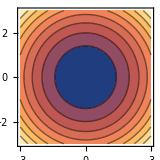

-Graphics3D-

```mathematica
ContourPlot[x^2+y^2,{x,-3,3},{y,-3,3}]
Plot3D[Which[x^2+y^2<=20,x^2+y^2],{x,-5,5},{y,-5,5},
		PlotPoints->200]
```

```mathematica
Limit[Limit[(x*y)/((x^2)+(y^2)),y->0],x->0]
```

0

Lo que obtenemos es un posible candidato a límite.

```mathematica
Limit[Limit[(x*y)/((x^2)+(y^2)),x->0],y->0]
Limit[(x*y)/((x^2)+(y^2))/.{x->0},y->0]
```

0

0

```mathematica
Limit[(x*y)/((x^2)+(y^2))/.{y->m*x},x->0]
```

m/(1+m^2)

```mathematica
Plot3D[(x*y)/((x^2)+(y^2)),{x,-3,3},{y,-3,3},PlotPoints->200]
```

-Graphics3D-

```mathematica
Plot3D[((x^3)*(y^2))/((x^6)+(y^4)),{x,-3,3},{y,-3,3},PlotPoints->200]
```

-Graphics3D-